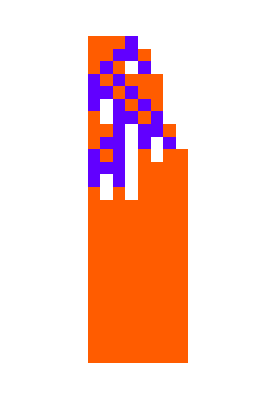

```mathematica
ArrayPlot[CellularAutomaton[{837428508144, 3, 1}, {Append[Table[1, 3], 2], 0}, {25, {-5, 12}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

```mathematica
RandomInteger[{0, 2}, 10]
```

{1,0,3,2,3,1,2,2,0,1}

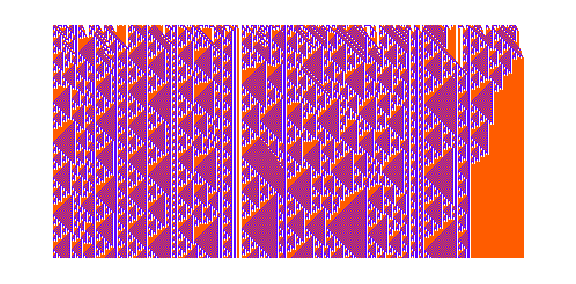

```mathematica
ArrayPlot[CellularAutomaton[{837428508144, 3, 1}, {RandomInteger[{0, 2}, 400], 0}, 200], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], ImageSize->Large]
```

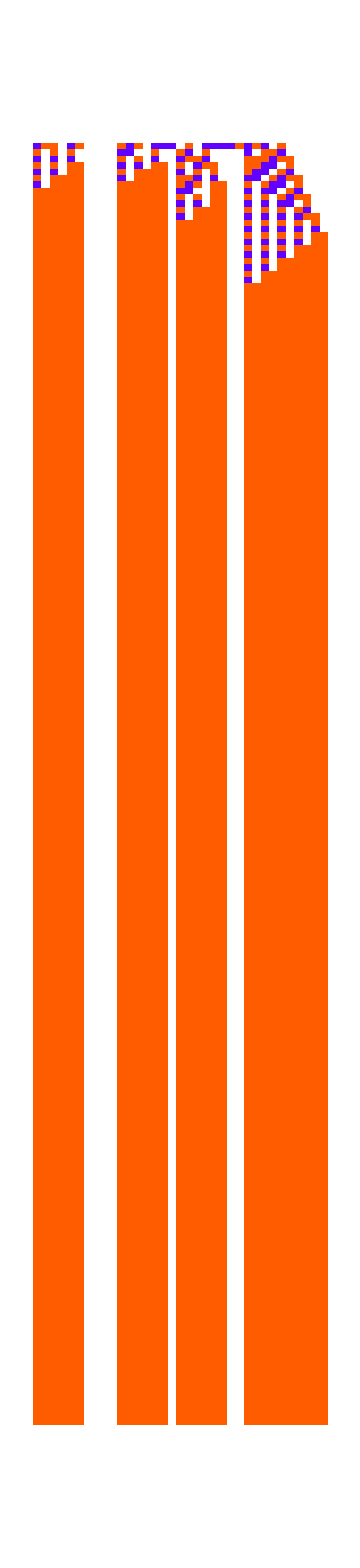
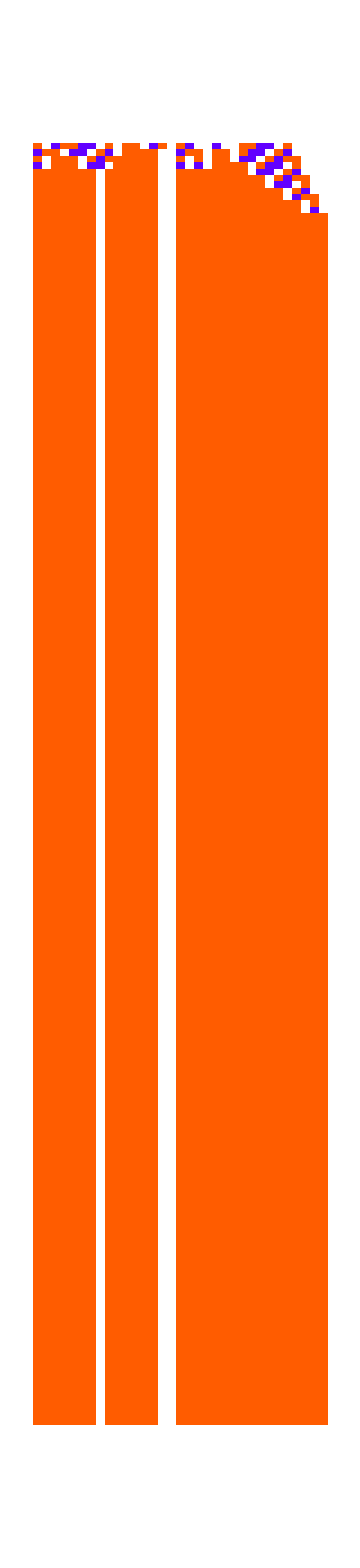
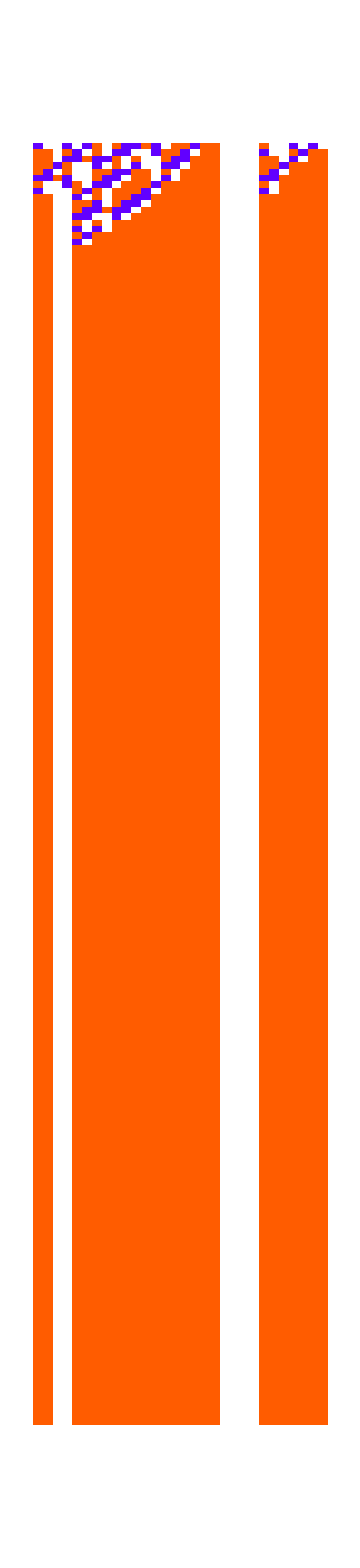
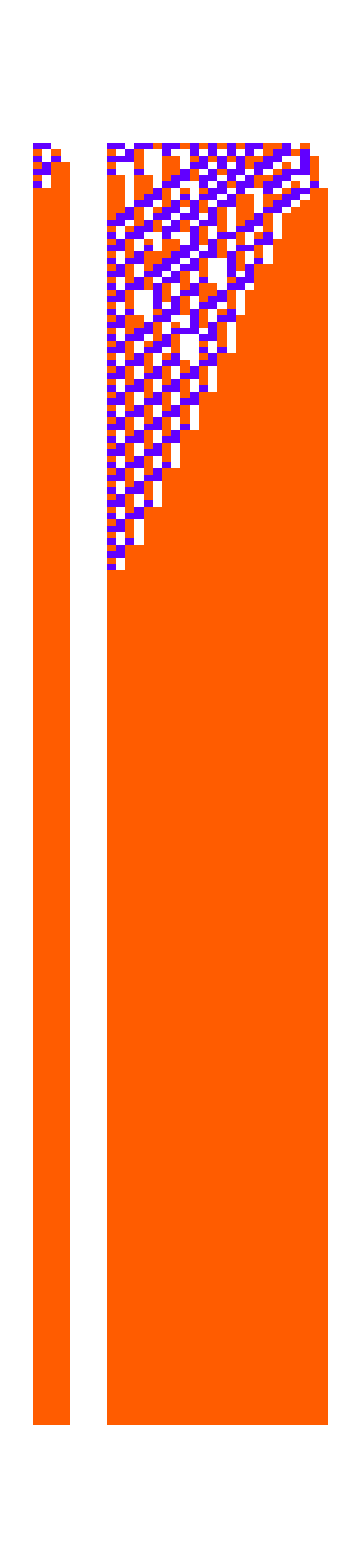
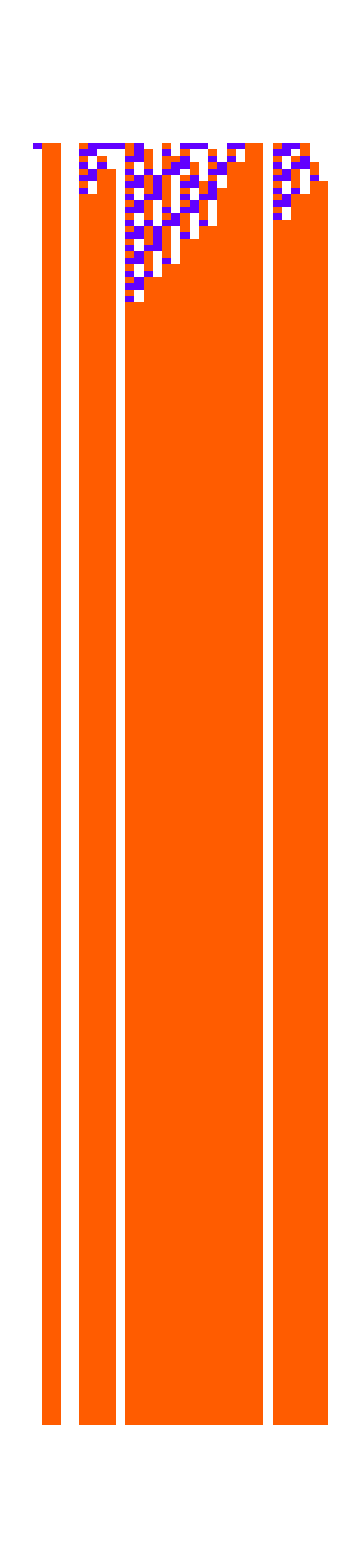
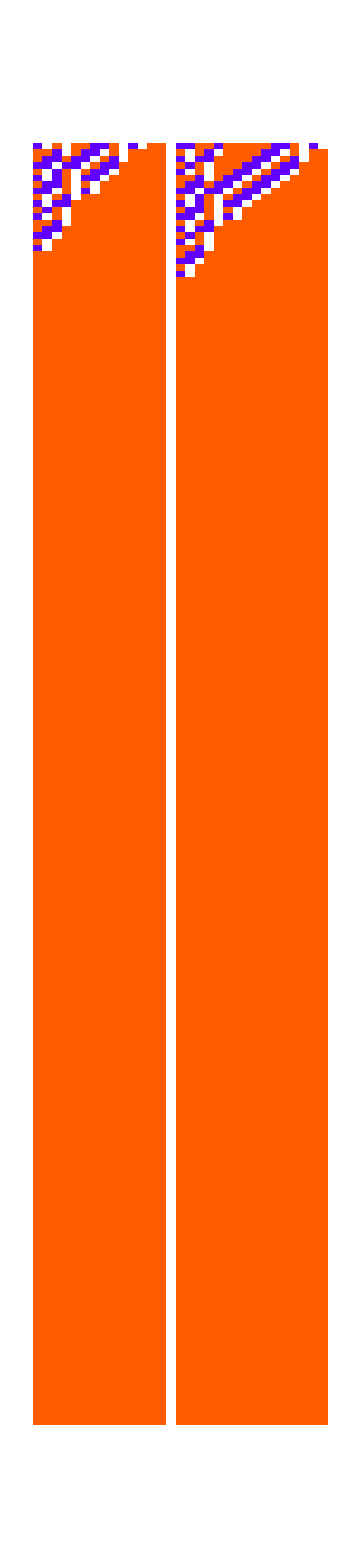
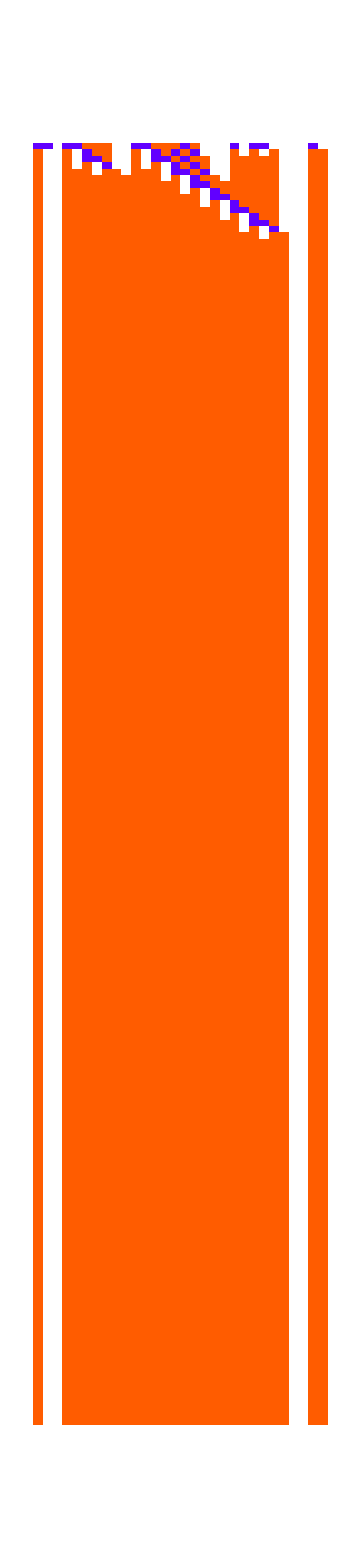
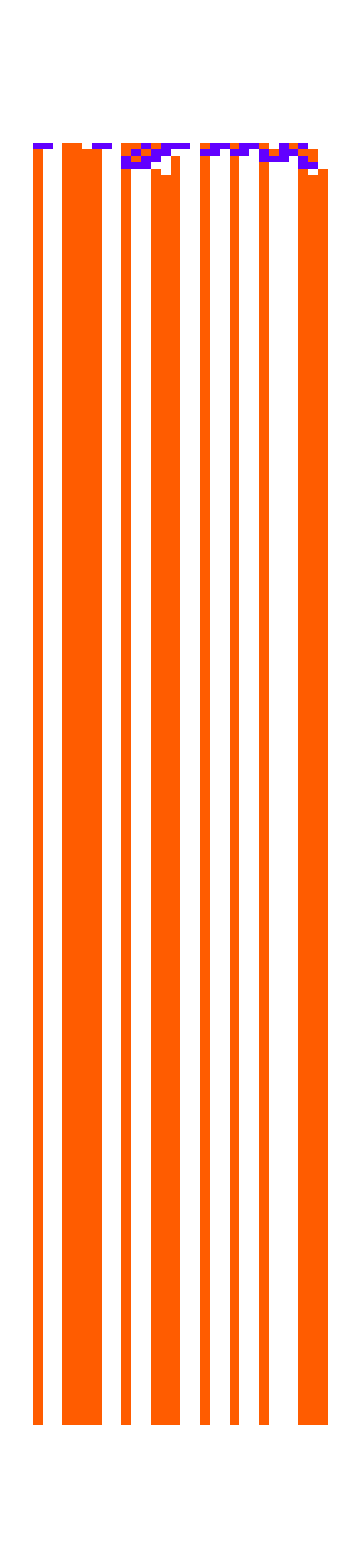

```mathematica
ArrayPlot[CellularAutomaton[{#, 3, 1}, {RandomInteger[{0, 2}, 30], 0}, {200, Automatic}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], ImageSize->Medium]&/@ {1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883}
```

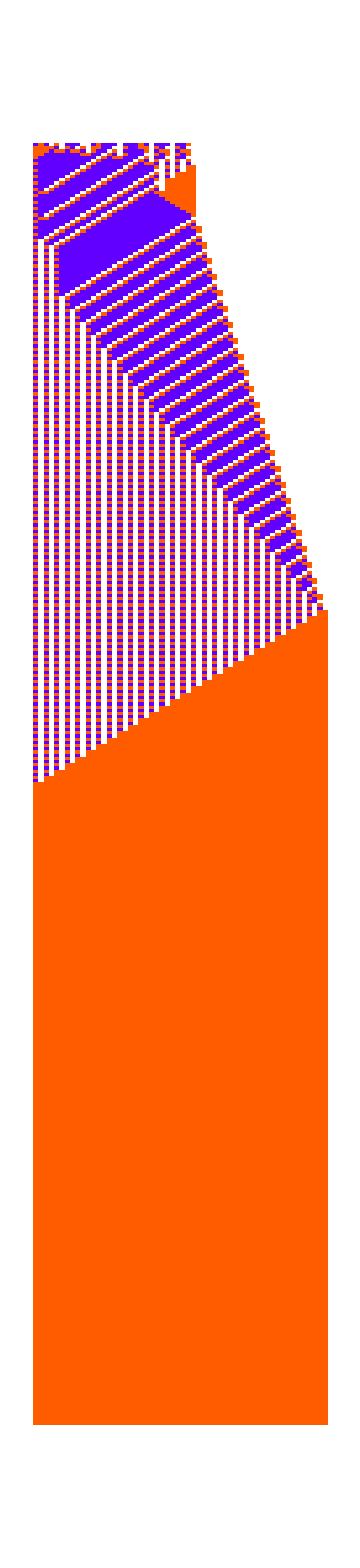

```mathematica
ArrayPlot[CellularAutomaton[{#, 3, 1}, {RandomInteger[{0, 2}, 30], 0}, {400, Automatic}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], ImageSize->Medium]&/@ {1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883}[[{-3}]]
```

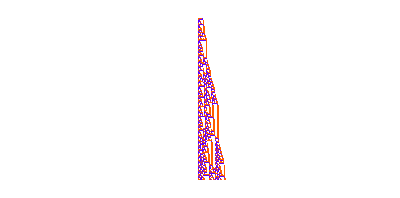
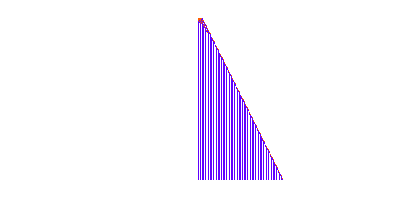
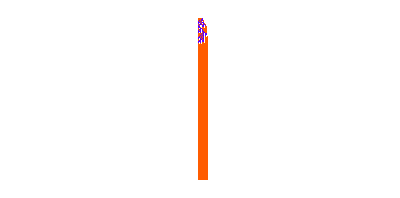
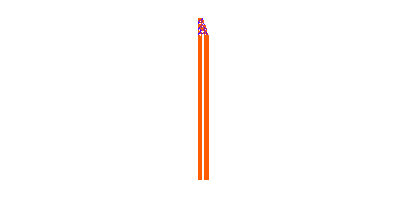
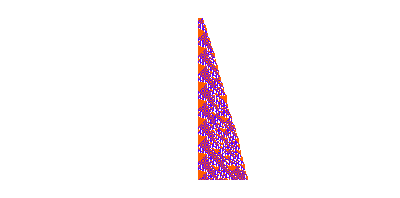
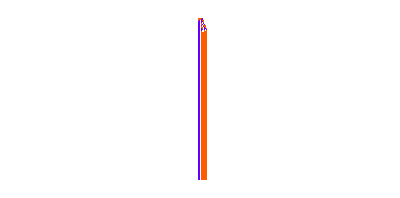
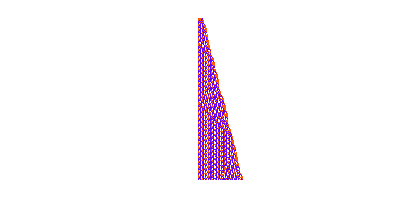
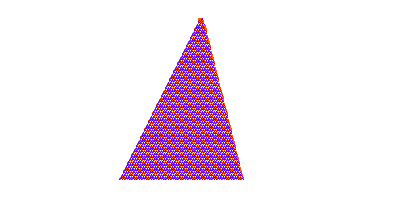
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
SeedRandom[111200+i];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{837428508144, 3, 1}],{Join[Table[1,4],{2}],0},{200,All}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"], ImageSize->Tiny], {i, 30}]
```

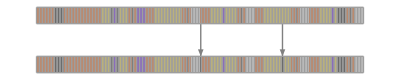

```mathematica
{{"[◼]", "RulesMutationPlot"}}[{{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{{"[◼]", "RandomRuleMutation"}}[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, 2]}]
```

```mathematica
Table[
SeedRandom[114770+i];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, 15],{Join[Table[1,4],{2}],0},{200,Automatic}],  ColorFunction->(If[# ==0, White, Blend[{Blue, LightBlue}, #]]& ),ImageSize->Small], {i, 300}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[113870+52];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, 10],{Join[Table[1,4],{2}],0},{2000,Automatic}],  ColorFunction->(If[# ==0, White, Blend[{Blue, LightBlue}, #]]& ),ImageSize->Small]
```

-Graphics-

```mathematica
Head/@
```

{Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics,Graphics}

```mathematica
SeedRandom[112070+2];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}],{Join[Table[1,4],{2}],0},{2000,Automatic}],  ColorFunction->(If[# ==0, White, Blend[{Blue, LightBlue}, #]]& ),ImageSize->Small]
```

-Graphics-

```mathematica
SeedRandom[111170+30];{{"[◼]", "RandomRuleMutation"}}[{837428508144, 3, 1}]
```

{837471554865,3,1}

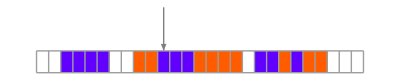

```mathematica
MapAt[{}&,{{"[◼]", "RulesMutationPlot"}}[{{837428508144, 3, 1}, {837471554865,3,1}}], {1,3,1}]
```

```mathematica
{{"[◼]", "RuleMutationsList"}}[{837428508144, 3, 1}]
```

{{3379294336473,3,1},{5921160164802,3,1},{1684717117587,3,1},{2532005727030,3,1},{272569435182,3,1},{554998971663,3,1},{649142150490,3,1},{743285329317,3,1},{774666388926,3,1},{806047448535,3,1},{816507801738,3,1},{826968154941,3,1},{840915292545,3,1},{844402076946,3,1},{838590769611,3,1},{839753031078,3,1},{837815928633,3,1},{837041087655,3,1},{837557648307,3,1},{837299367981,3,1},{837471554865,3,1},{837385461423,3,1},{837399810330,3,1},{837414159237,3,1},{837418942206,3,1},{837423725175,3,1},{837430102467,3,1},{837426913821,3,1},{837429039585,3,1},{837427976703,3,1},{837428685291,3,1},{837428330997,3,1},{837428567193,3,1},{837428449095,3,1},{837428527827,3,1},{837428547510,3,1},{837428495022,3,1},{837428501583,3,1},{837428503770,3,1},{837428505957,3,1},{837428508873,3,1},{837428507415,3,1},{837428507658,3,1},{837428507901,3,1},{837428508225,3,1},{837428508063,3,1},{837428508171,3,1},{837428508117,3,1},{837428508153,3,1},{837428508162,3,1},{837428508147,3,1},{837428508150,3,1}}

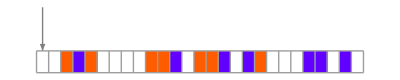

```mathematica
MapAt[{}&,{{"[◼]", "RulesMutationPlot"}}[{{5586032021307,3,1},{502300364649,3,1}}]
,{1,3,1}]
```

```mathematica
Take[{{"[◼]", "RuleMutationsList"}}[{5586032021307,3,1}],8]
```

{{502300364649,3,1},{3044166192978,3,1},{6433320630750,3,1},{7280609240193,3,1},{5868461557788,3,1},{5303602484826,3,1},{5397745663653,3,1},{5491888842480,3,1}}

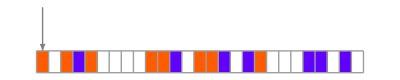
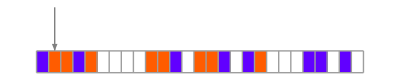
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Style[MapAt[{}&,{{"[◼]", "RulesMutationPlot"}}[{{5586032021307,3,1},#}]
,{1,3,1}]&/@Take[{{"[◼]", "RuleMutationsList"}}[{5586032021307,3,1}],8],LineSpacing->{1.2,0}]
```

```mathematica
Module[
{deep=100,cut=200,ru,life},
SeedRandom[426778];
{{"[◼]", "RulesMutationPlot"}}[
Take[First/@Split[First/@NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]
],{48,50}]]]
```

```mathematica
GraphicsRow[Table[
SeedRandom[111170+30];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{837428508144, 3, 1}],{Join[Table[1,4],{2}],0},{{1000*i, 1000*(i+1)},Automatic}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]],{i,0, 5}] ]
```

-Graphics-

```mathematica
GraphicsRow[Table[
SeedRandom[111170+30];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{837428508144, 3, 1}],{Join[Table[1,4],{2}],0},{{1000*i, 1000*(i+1)},Automatic}], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]],{i,0, 4}] ]
```

-Graphics-

```mathematica
Table[
ArrayPlot[CellularAutomaton[{837471554865,3,1},{RandomInteger[{0, 2}, 10],0},{200,All}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]],{i,0, 5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Hero

-Graphics-

```mathematica
GraphicsColumn[{{{"[◼]", "RulesMutationPlot"}}[{{837428508144, 3, 1}}],ArrayPlot[CellularAutomaton[{837428508144, 3, 1}, {Append[Table[1, 3], 2], 0}, {25, {-5, 12}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]}]
```

-Graphics-

```mathematica
Table[
ArrayPlot[CellularAutomaton[{837471554865,3,1},{Append[Table[1, i], 2],0},{30,{-5, 20}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]],{i,3, 8, 2}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
ArrayPlot[CellularAutomaton[{837428508144, 3, 1},{Append[Table[1, i], 2],0},{40,{-5, 20}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]],{i,3, 8, 2}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{ru={2775499274778,3,1}},GraphicsRow[
{RulePlot[CellularAutomaton[ru],ColorRules->{0->GrayLevel[1],1->RGBColor[0.7547083274999999, 0.085295375, 0.2080375],2->Hue[0.53, 1, 1]},
MeshStyle->Opacity[.2],ImageSize->280],ArrayPlot[CellularAutomaton[ru,CenterArray[{1},20],43],
ColorRules->{0->GrayLevel[1],1->RGBColor[0.7547083274999999, 0.085295375, 0.2080375],2->Hue[0.53, 1, 1]},
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]},Spacings->40]]
```

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,10],{2}],0},{75,{-5, 30}}, 1], "Trim"->{None, None}, ImageSize->Medium,ColorRules->{0->GrayLevel[1],1->RGBColor[0.7547083274999999, 0.085295375, 0.2080375],2->Hue[0.53, 1, 1]},  ColorFunction->(Blend[{White, Blue}, #]&)]
```

-Graphics-

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, {}], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)]
```

-Graphics-

```mathematica
Table[
SeedRandom[111090+i];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, {RandomChoice[#[[;;1]]]&, RandomChoice}, "Body"->True], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)], {i, 30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
SeedRandom[111180+i];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, 1, "Body"->True], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)], {i, 30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
SeedRandom[111090+i];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{{"[◼]", "RandomRuleMutation"}}[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}],{Join[Table[1,3],{2}],0},{50,{-5, 15}}, {}, "Body"->True], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)], {i, 30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[111090+16];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, 1, "Body"->True], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)]
```

-Graphics-

```mathematica
SeedRandom[111060+8];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, #, "Body"->True], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)]&/@ {<||>, ({RandomChoice[#[[;;1]]]&, RandomChoice})}
```

{-Graphics-,-Graphics-}

```mathematica
SeedRandom[111000+17];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)] &/@ {<||>, 1}
```

{-Graphics-,-Graphics-}

```mathematica
SeedRandom[111090+16];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)] &/@ {<||>, 1}
```

{-Graphics-,-Graphics-}

```mathematica
SeedRandom[111090+30];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)] &/@ {<||>, 1}
```

{-Graphics-,-Graphics-}

```mathematica
SeedRandom[111180+3];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)] &/@ {<||>, <|{5,6}->5|>}
```

{-Graphics-,-Graphics-}

```mathematica
SeedRandom[111180+3];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)] &/@ {<||>, 1}
```

```mathematica
Table[
SeedRandom[111180+3];{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,i],{2}],0},{100,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Automatic,   ColorFunction->(If[# == 0, White, If[# == 1/5,Darker[Blue], Blend[{White, LightBlue, Blue}, #]]]&)], {i,1, 5}]&/@ {<||>, <|{5,6}->5|>}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,i],{2}],0},{50,{-5, 15}}, #], "Trim"->{None, None}, ImageSize->Medium,ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/6], {i, 2, 5}]]], {i,1, 5}]&/@ {<||>, <|{5,6}->5|>}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SeedRandom[111180+3];ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, 1]
```

{{{0,0,0,0,0,1,1,1,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,4,3,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,4,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,2,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,5,1,2,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,3,3,3,0,0,0,0,0,0,0,0,0,0,0}},<|{5,6}→5|>}

```mathematica
cols =Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/6], {i, 2, 5}]]
```

{0→GrayLevel[1],1→RGBColor[0, 0, Rational[2, 3]],2→RGBColor[0.9133333333333333, 0.96, 1.],3→RGBColor[0.87, 0.94, 1],4→RGBColor[0.5800000000000001, 0.6266666666666667, 1],5→RGBColor[0.29000000000000004, 0.31333333333333335, 1]}

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{50,{-5, 15}}, <|{5,6}->5|>],"Trim"->{None, None}, ImageSize->Medium,ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/6], {i, 2, 5}]]]
```

-Graphics-